```mathematica
单个圆线圈的电场分布
```

```mathematica
Integrate[1/(√(a-b Cos[φ])),{φ,0,2π},
Assumptions->a>b>0]
```

(2 (√(a+b) -(2 b)/(a-b)+√(a-b) (2 b)/(a+b)))/(√(a^2-b^2))

```mathematica
观察椭圆积分的性质
```

```mathematica
Limit[EllipticK[x],x->1]
```

∞

```mathematica
Limit[EllipticK[x],x->-∞]
```

0

```mathematica
EllipticK[0]
```

π/2

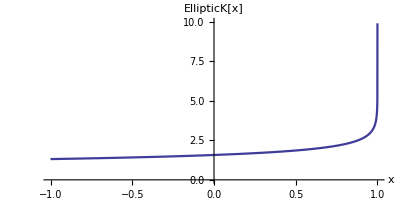

```mathematica
Plot[EllipticK[x],{x,-1,1},PlotRange->{0,10},
AxesStyle->Thickness[0.003],
PlotStyle->Thickness[0.004],AspectRatio->0.5,
AxesLabel->{"x","EllipticK[x]"}]
```